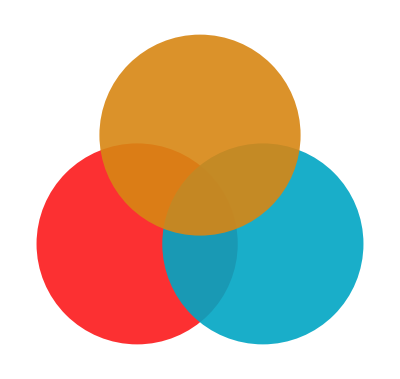

```mathematica
L = 1;
R = 0.8* L;
α = 0.9;
norm[v_]:=Module[{n, i , l},l =Length[v];  n =√Sum[v[[i]]^2, {i, 1, l}] ;v/n];

col1 = {194, 19, 21};col1N = norm[col1];
col2 = {0, 177, 209};col2N = norm[col2];
col3 = {252, 156, 22};col3N = norm[col3];
c1  = Graphics[{Opacity[α],RGBColor[col1N[[1]], col1N[[2]], col1N[[3]]], Disk[{0, 0}, R]}];
c2  = Graphics[{Opacity[α],RGBColor[col2N[[1]], col2N[[2]], col2N[[3]]], Disk[{L, 0}, R]}];
c3  = Graphics[{Opacity[α],RGBColor[col3N[[1]], col3N[[2]], col3N[[3]]], Disk[{L/2, √3 L/2}, R]}];
c = Show[{c1, c2, c3}]
```

```mathematica
base = 24;
coef = {1, 1.5, 2, 3, 4};
dirnames = {"mipmap-mdpi", "mipmap-hdpi", "mipmap-xhdpi", "mipmap-xxhdpi", "mipmap-xxxhdpi"}
Show[c, ImageSize->Tiny]
For[i = 1, i≤ Length[dirnames], i++,Export[ "c:\\Users\\Andrea\\Documents\\res\\"<>dirnames[[i]]<>"\\circles.png", c, ImageSize ->base*coef[[i]], Background->None]]
```

{mipmap-mdpi,mipmap-hdpi,mipmap-xhdpi,mipmap-xxhdpi,mipmap-xxxhdpi}

-Graphics-